```mathematica
Needs["PlotLegends`"]
```

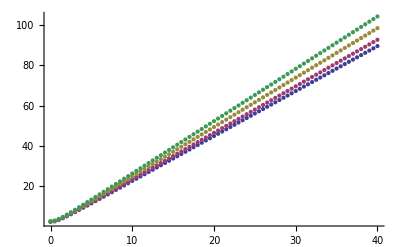

```mathematica
f01r=ListPlot[{Import["Dropbox/Trabalhos/free expansion vortices/data/R-l0-lam01.dat","Table"],Import["Dropbox/Trabalhos/free expansion vortices/data/R-l1-lam01.dat","Table"],Import["Dropbox/Trabalhos/free expansion vortices/data/R-l2-lam01.dat","Table"],Import["Dropbox/Trabalhos/free expansion vortices/data/R-l3-lam01.dat","Table"]}]
```

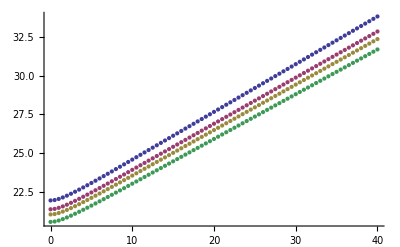

```mathematica
f01z=ListPlot[{Import["Dropbox/Trabalhos/free expansion vortices/data/Z-l0-lam01.dat","Table"],Import["Dropbox/Trabalhos/free expansion vortices/data/Z-l1-lam01.dat","Table"],Import["Dropbox/Trabalhos/free expansion vortices/data/Z-l2-lam01.dat","Table"],Import["Dropbox/Trabalhos/free expansion vortices/data/Z-l3-lam01.dat","Table"]}]
```

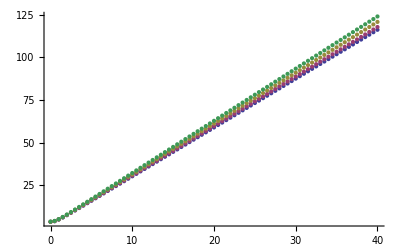

```mathematica
f00r=ListPlot[{Import["Dropbox/Trabalhos/free expansion vortices/data/R-l0-lam00.dat","Table"],Import["Dropbox/Trabalhos/free expansion vortices/data/R-l1-lam00.dat","Table"],Import["Dropbox/Trabalhos/free expansion vortices/data/R-l2-lam00.dat","Table"],Import["Dropbox/Trabalhos/free expansion vortices/data/R-l3-lam00.dat","Table"]}]
```

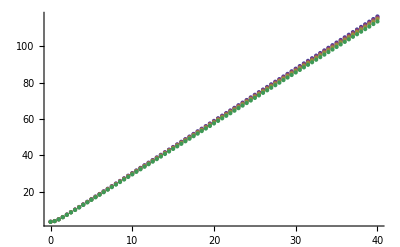

```mathematica
f00z=ListPlot[{Import["Dropbox/Trabalhos/free expansion vortices/data/Z-l0-lam00.dat","Table"],Import["Dropbox/Trabalhos/free expansion vortices/data/Z-l1-lam00.dat","Table"],Import["Dropbox/Trabalhos/free expansion vortices/data/Z-l2-lam00.dat","Table"],Import["Dropbox/Trabalhos/free expansion vortices/data/Z-l3-lam00.dat","Table"]}]
```

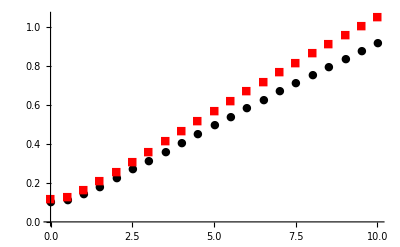

```mathematica
f01=ListPlot[{Table[{(i-1)*0.5,Import["Dropbox/Trabalhos/free expansion vortices/data/R-l0-lam01.dat","Table"][[i,2]]/Import["Dropbox/Trabalhos/free expansion vortices/data/Z-l0-lam01.dat","Table"][[i,2]]},{i,1,21,1}],Table[{(i-1)*0.5,Import["Dropbox/Trabalhos/free expansion vortices/data/R-l2-lam01.dat","Table"][[i,2]]/Import["Dropbox/Trabalhos/free expansion vortices/data/Z-l2-lam01.dat","Table"][[i,2]]},{i,1,21,1}]},PlotStyle->{Black,Red},PlotMarkers->{Automatic,Tiny}]
```

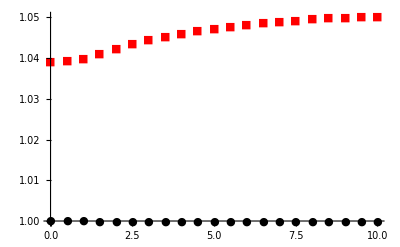

```mathematica
f00=ListPlot[{Table[{(i-1)*0.5,Import["Dropbox/Trabalhos/free expansion vortices/data/R-l0-lam00.dat","Table"][[i,2]]/Import["Dropbox/Trabalhos/free expansion vortices/data/Z-l0-lam00.dat","Table"][[i,2]]},{i,1,21,1}],Table[{(i-1)*0.5,Import["Dropbox/Trabalhos/free expansion vortices/data/R-l2-lam00.dat","Table"][[i,2]]/Import["Dropbox/Trabalhos/free expansion vortices/data/Z-l2-lam00.dat","Table"][[i,2]]},{i,1,21,1}]},PlotStyle->{Black,Red},PlotMarkers->{Automatic,Tiny}]
```

```mathematica
eqs1=r0==1/r0^3+(Gamma[2*L+1]/(Gamma[L+1]*Gamma[L+2]))*(γ/(2^(2*L-1)*Sqrt[2*π]*r0^3*z0))
eqs2=λ^2*z0==1/z0^3+(Gamma[2*L+1]/(Gamma[L+1]*Gamma[L+1]))*(γ/(2^(2*L-1)*Sqrt[2*π]*r0^2*z0^2))
exp1=D[R[t],{t,2}]==1/R[t]^3+(γ*(L+1)*Gamma[2*L+1])/(2^(2*L-1)*Sqrt[2*π]*Gamma[L+2]^2*R[t]^3*Z[t])
exp2=D[Z[t],{t,2}]==1/Z[t]^3+(γ*Gamma[2*L+1])/(2^(2*L-1)*Sqrt[2*π]*Gamma[L+1]^2*R[t]^2*Z[t]^2)
A[L_,t_]:=(R[t]*Sqrt[L+1])/Z[t]
A0[t_]:=R[t]/Z[t]
```

r0==1/r0^3+(2^(1/2-2 L) γ Gamma[1+2 L])/(√π r0^3 z0 Gamma[1+L] Gamma[2+L])

z0 λ^2==1/z0^3+(2^(1/2-2 L) γ Gamma[1+2 L])/(√π r0^2 z0^2 Gamma[1+L]^2)

R''[t]==1/R[t]^3+(2^(1/2-2 L) (1+L) γ Gamma[1+2 L])/(√π Gamma[2+L]^2 R[t]^3 Z[t])

Z''[t]==1/Z[t]^3+(2^(1/2-2 L) γ Gamma[1+2 L])/(√π Gamma[1+L]^2 R[t]^2 Z[t]^2)

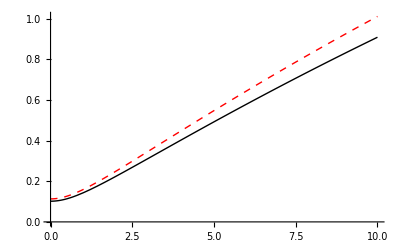

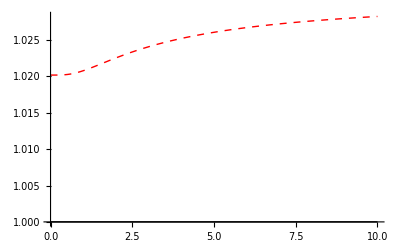

```mathematica
λ=0.1;
γ=800;
s0=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,Derivative[1][R][0]==0,Derivative[1][Z][0]==0}/.L->0/.FindRoot[{eqs1,eqs2}/.L->0,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s1=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,Derivative[1][R][0]==0,Derivative[1][Z][0]==0}/.L->1/.FindRoot[{eqs1,eqs2}/.L->1,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s2=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,Derivative[1][R][0]==0,Derivative[1][Z][0]==0}/.L->2/.FindRoot[{eqs1,eqs2}/.L->2,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s3=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,Derivative[1][R][0]==0,Derivative[1][Z][0]==0}/.L->3/.FindRoot[{eqs1,eqs2}/.L->3,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
f01t=Plot[{A0[t]/.s0,A[2,t]/.s2},{t,0,10},PlotStyle->{Black,Directive[Red,Dashed]}]
ClearAll[λ,γ,s0,s1,s2,s3]
λ=1;
γ=800;
s0=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,Derivative[1][R][0]==0,Derivative[1][Z][0]==0}/.L->0/.FindRoot[{eqs1,eqs2}/.L->0,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s1=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,Derivative[1][R][0]==0,Derivative[1][Z][0]==0}/.L->1/.FindRoot[{eqs1,eqs2}/.L->1,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s2=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,Derivative[1][R][0]==0,Derivative[1][Z][0]==0}/.L->2/.FindRoot[{eqs1,eqs2}/.L->2,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s3=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,Derivative[1][R][0]==0,Derivative[1][Z][0]==0}/.L->3/.FindRoot[{eqs1,eqs2}/.L->3,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
f00t=Plot[{A0[t]/.s0,A[2,t]/.s2},{t,0,10},PlotStyle->{Black,Directive[Red,Dashed]}]
ClearAll[λ,γ,s0,s1,s2,s3,R]
```

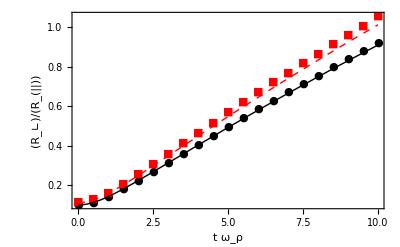

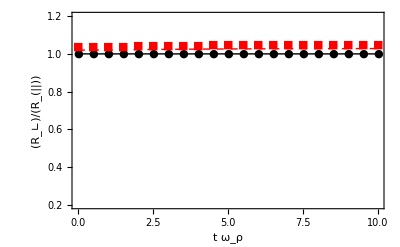

```mathematica
num01=Show[f01,f01t,PlotRange->All,RotateLabel->False,FrameLabel->{t*Subscript[ω,ρ],Subscript[R,"∟"]/Subscript[R,"||"]},LabelStyle->{Medium},Axes->False,Frame->True]
num00=Show[f00,f00t,PlotRange->{{0,10},{0.2,1.2}},RotateLabel->False,FrameLabel->{Subscript[ω,ρ]*t,Subscript[R,"∟"]/Subscript[R,"||"]},LabelStyle->{Medium},Axes->False,Frame->True]
```

```mathematica
Export["Dropbox/Trabalhos/free expansion vortices/data/num01.eps",num01]
Export["Dropbox/Trabalhos/free expansion vortices/data/num00.eps",num00]
Export["Dropbox/Trabalhos/free expansion vortices/num01.eps",num01]
Export["Dropbox/Trabalhos/free expansion vortices/num00.eps",num00]
```

Dropbox/Trabalhos/free expansion vortices/data/num01.eps

Dropbox/Trabalhos/free expansion vortices/data/num00.eps

Dropbox/Trabalhos/free expansion vortices/num01.eps

Dropbox/Trabalhos/free expansion vortices/num00.eps